```mathematica
ClearAll["Global`*"]
```

```mathematica
F1[α_,γ_,k_,σ_,L_,q_]=q*α(1+α)(1+γ)^2/(L+(1+α)^2(1+γ)^2)-k*γ
```

(α (α+1) (γ+1)^2 q)/((α+1)^2 (γ+1)^2+L)-γ k

```mathematica
F2[α_,γ_,k_,σ_,L_,q_]=-q*α(1+α)(1+γ)^2/(L+(1+α)^2(1+γ)^2)+σ
```

σ-(α (α+1) (γ+1)^2 q)/((α+1)^2 (γ+1)^2+L)

```mathematica
s=NDSolve[{α'[t]==F2[α[t],γ[t],1,2,7.5*10^6,20],γ'[t]==F1[α[t],γ[t],1,2,7.5*10^6,20],α[0]==200,γ[0]==1},{α,γ},{t,3700}]
```

{{α→InterpolatingFunction[(0. | 3700.),<>],γ→InterpolatingFunction[(0. | 3700.),<>]}}

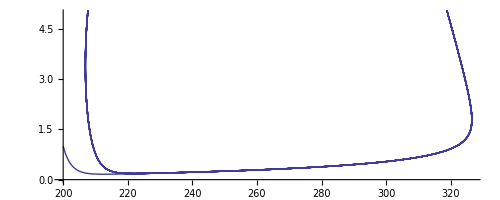

```mathematica
ParametricPlot[Evaluate[{α[t],γ[t]}/.s],{t,0,700}]
```

```mathematica
F1[α_,γ_,k_,σ_,L_,q_]=q*α(1+α)(1+γ)^2/(L+(1+α)^2(1+γ)^2)-k*γ
```

(α (α+1) (γ+1)^2 q)/((α+1)^2 (γ+1)^2+L)-γ k

```mathematica
TeXForm[(α (α+1) (γ+1)^2 q)/((α+1)^2 (γ+1)^2+L)-kγ]
```

\frac{\alpha  (\alpha +1) (\gamma +1)^2 q}{(\alpha +1)^2 (\gamma +1)^2+L}-\text{k$\gamma $}

```mathematica
F2[α_,γ_,k_,σ_,L_,q_]=-q*α(1+α)(1+γ)^2/(L+(1+α)^2(1+γ)^2)+σ
```

σ-(α (α+1) (γ+1)^2 q)/((α+1)^2 (γ+1)^2+L)

```mathematica
Reduce[{0 == F1[α,γ,k,σ,L,q], 0 ==F2[α,γ,k,σ,L,q]}, {γ,α}]
```

(σ==0∧q==0∧k==0∧α^2 γ^2+2 α^2 γ+α^2+2 α γ^2+4 α γ+2 α+γ^2+2 γ+L+1≠0)∨(σ==0∧q==0∧γ==0∧α^2 k+2 α k+k L+k≠0)∨(σ==0∧k==0∧q≠0∧γ==-1∧L≠0)∨(σ==0∧k==0∧(γ+1) q≠0∧(α==-1∨α==0)∧α γ^2+2 α γ+α+γ^2+2 γ+L+1≠0)∨(k≠0∧γ==σ/k∧(γ+1) (q-σ)≠0∧(α==(2 γ^2 σ+4 γ σ-(γ+1) √(4 L q σ-4 L σ^2+γ^2 q^2+2 γ q^2+q^2)+γ^2 (-q)-2 γ q-q+2 σ)/(2 (-γ^2 σ-2 γ σ+γ^2 q+2 γ q+q-σ))∨α==(2 γ^2 σ+4 γ σ+(γ+1) √(4 L q σ-4 L σ^2+γ^2 q^2+2 γ q^2+q^2)+γ^2 (-q)-2 γ q-q+2 σ)/(2 (-γ^2 σ-2 γ σ+γ^2 q+2 γ q+q-σ)))∧-γ^2 k^2 L σ-2 γ k^2 L σ+γ^2 k^2 L q+2 γ k^2 L q+k^2 L q+α γ^2 k^2 q+2 α γ k^2 q+α k^2 q+γ^2 k^2 q+2 γ k^2 q+k^2 q+2 k L σ^2+2 α γ^2 k q σ+4 α γ k q σ+2 α k q σ+2 γ^2 k q σ+4 γ k q σ+2 k q σ+L σ^3+α γ^2 q σ^2+2 α γ q σ^2+α q σ^2+γ^2 q σ^2+2 γ q σ^2+q σ^2≠0)∨(q==σ∧k≠0∧γ==σ/k∧γ (γ+1)≠0∧α==(-γ^2-2 γ-L-1)/(γ+1)^2∧k^2 L^2+γ^4 k^2 L+4 γ^3 k^2 L+6 γ^2 k^2 L+4 γ k^2 L+k^2 L+2 k L^2 σ+L^2 σ^2≠0)

```mathematica
J=D[{F2[α,γ,k,σ,L,q], F1[α,γ,k,σ,L,q]},{{α,γ}}]
```

((2 q α (α+1)^2 (γ+1)^4)/(((α+1)^2 (γ+1)^2+L)^2)-(q α (γ+1)^2)/((α+1)^2 (γ+1)^2+L)-(q (α+1) (γ+1)^2)/((α+1)^2 (γ+1)^2+L) | (2 q α (α+1)^3 (γ+1)^3)/(((α+1)^2 (γ+1)^2+L)^2)-(2 q α (α+1) (γ+1))/((α+1)^2 (γ+1)^2+L)
-(2 q α (α+1)^2 (γ+1)^4)/(((α+1)^2 (γ+1)^2+L)^2)+(q α (γ+1)^2)/((α+1)^2 (γ+1)^2+L)+(q (α+1) (γ+1)^2)/((α+1)^2 (γ+1)^2+L) | -(2 q α (α+1)^3 (γ+1)^3)/(((α+1)^2 (γ+1)^2+L)^2)+(2 q α (α+1) (γ+1))/((α+1)^2 (γ+1)^2+L)-k)

```mathematica
Simplify[J]
```

(-(q (γ+1)^2 ((α+1)^2 (γ+1)^2+L+2 L α))/(((α+1)^2 (γ+1)^2+L)^2) | -(2 L q α (α+1) (γ+1))/(((α+1)^2 (γ+1)^2+L)^2)
(q (γ+1)^2 ((α+1)^2 (γ+1)^2+L+2 L α))/(((α+1)^2 (γ+1)^2+L)^2) | -(2 q α (α+1)^3 (γ+1)^3)/(((α+1)^2 (γ+1)^2+L)^2)+(2 q α (α+1) (γ+1))/((α+1)^2 (γ+1)^2+L)-k)

```mathematica
TeXForm[Simplify[J]]
```

\left(
\begin{array}{cc}
 -\frac{q (\gamma +1)^2 \left((\alpha +1)^2 (\gamma +1)^2+L+2 L \alpha \right)}{\left((\alpha +1)^2 (\gamma +1)^2+L\right)^2} & -\frac{2 L q \alpha 
   (\alpha +1) (\gamma +1)}{\left((\alpha +1)^2 (\gamma +1)^2+L\right)^2} \\
 \frac{q (\gamma +1)^2 \left((\alpha +1)^2 (\gamma +1)^2+L+2 L \alpha \right)}{\left((\alpha +1)^2 (\gamma +1)^2+L\right)^2} & -\frac{2 q \alpha  (\alpha
   +1)^3 (\gamma +1)^3}{\left((\alpha +1)^2 (\gamma +1)^2+L\right)^2}+\frac{2 q \alpha  (\alpha +1) (\gamma +1)}{(\alpha +1)^2 (\gamma +1)^2+L}-k \\
\end{array}
\right)

```mathematica
γ=σ/k
```

σ/k

```mathematica
TeXForm[γ]
```

\frac{\sigma }{k}

```mathematica
α=Simplify[(2 γ^2 σ+4 γ σ-(γ+1) √(4 L q σ-4 L σ^2+γ^2 q^2+2 γ q^2+q^2)+γ^2 (-q)-2 γ q-q+2 σ)/(2 (-γ^2 σ-2 γ σ+γ^2 q+2 γ q+q-σ))]
```

(σ (2 σ-q)-k (√((q^2 (k+σ)^2)/k^2+4 L q σ-4 L σ^2)+q-2 σ))/(2 (k+σ) (q-σ))

```mathematica
TeXForm[Expand[σ (2 σ-q)+k (√((q^2 (k+σ)^2)/k^2+4 L q σ-4 L σ^2)+q-2 σ)]/(2 (k+σ) (q-σ))]
```

\frac{k \sqrt{\frac{q^2 (k+\sigma )^2}{k^2}+4 L q \sigma -4 L \sigma ^2}+k q-2 k \sigma -q \sigma +2 \sigma ^2}{2 (k+\sigma ) (q-\sigma )}

```mathematica
Reduce[{0<α,k>0,σ>0,L>0,q>0},{k,σ,L,q}]
```

False

```mathematica
Reduce[{0<α,γ>0,k>0,σ>0,L>0},{k,σ,L}]
```

False

```mathematica
J
```

((q (σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2))) ((σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2)))/(2 (q-σ) (k+σ))+1)^2 (σ/k+1)^4)/((q-σ) (k+σ) ((σ/k+1)^2 ((σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2)))/(2 (q-σ) (k+σ))+1)^2+L)^2)-(q (σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2))) (σ/k+1)^2)/(2 (q-σ) (k+σ) ((σ/k+1)^2 ((σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2)))/(2 (q-σ) (k+σ))+1)^2+L))-(q ((σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2)))/(2 (q-σ) (k+σ))+1) (σ/k+1)^2)/((σ/k+1)^2 ((σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2)))/(2 (q-σ) (k+σ))+1)^2+L) | (q (σ/k+1)^3 (σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2))) ((σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2)))/(2 (q-σ) (k+σ))+1)^3)/((q-σ) (k+σ) ((σ/k+1)^2 ((σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2)))/(2 (q-σ) (k+σ))+1)^2+L)^2)-(q (σ/k+1) (σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2))) ((σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2)))/(2 (q-σ) (k+σ))+1))/((q-σ) (k+σ) ((σ/k+1)^2 ((σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2)))/(2 (q-σ) (k+σ))+1)^2+L))
-(q (σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2))) ((σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2)))/(2 (q-σ) (k+σ))+1)^2 (σ/k+1)^4)/((q-σ) (k+σ) ((σ/k+1)^2 ((σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2)))/(2 (q-σ) (k+σ))+1)^2+L)^2)+(q (σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2))) (σ/k+1)^2)/(2 (q-σ) (k+σ) ((σ/k+1)^2 ((σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2)))/(2 (q-σ) (k+σ))+1)^2+L))+(q ((σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2)))/(2 (q-σ) (k+σ))+1) (σ/k+1)^2)/((σ/k+1)^2 ((σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2)))/(2 (q-σ) (k+σ))+1)^2+L) | -(q (σ/k+1)^3 (σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2))) ((σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2)))/(2 (q-σ) (k+σ))+1)^3)/((q-σ) (k+σ) ((σ/k+1)^2 ((σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2)))/(2 (q-σ) (k+σ))+1)^2+L)^2)+(q (σ/k+1) (σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2))) ((σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2)))/(2 (q-σ) (k+σ))+1))/((q-σ) (k+σ) ((σ/k+1)^2 ((σ (2 σ-q)-k (q-2 σ+√(-4 L σ^2+4 L q σ+(q^2 (k+σ)^2)/k^2)))/(2 (q-σ) (k+σ))+1)^2+L))-k)